# Collision I

## Lab Report

Names: Aryan Malhotra
Section: H4
Date: 10/09/2024

## Purpose

To investigate the relationship of impulse to change of momentum

## Readings

You can explore the Wikipedia or your favorite mechanics textbook,
Elastic collision, Inelastic collision, Kinematics, kinematics equations, Impulse

### Theory and concepts in short

In a collision it is difficult to use Newton’s Second Law, F = ma, because the force varies with time in some generally unknown manner (note: a bold letter for F means it is a vector unlike mass, m, which is a scalar).
We can rewrite the Newton’s second law in a manner more useful for collisions by using the impulse: I = ∫ F dt.
Integrating both sides of the second law,

 I = ∫ F dt = ∫ m a dt = ∫ m dv/dt dt =∫ m dv = m v_f - m v_i,
 
 where v_f and v_i are the velocities of mass m after and before the collision, respectively. Note that F is the total (net) force acting on the body. We define the linear momentum of m as P = mv. The second Newton’s law states that the change of momentum of a body during a collision is equal to the impulse it receives,
 
 I = ΔP.

## Procedure

### Procedure for Part I

When a dropped ball hits an object, it exerts a force on this object (and, by Newton’s third law, an equal but opposite in direction force is exerted on the ball). We will use the force probe to measure this force. You will be dropping a play-doh (or, clay) ball and a golf ball (of the same mass and from the same height). The golf ball undergoes a nearly elastic (energy conserving) collision, while the play-doh ball experiences an inelastic collision, in which its kinetic energy is fully converted to thermal energy (heat).

### Setting Up the Data Collection Program LoggerPro

- Load the computer program LoggerPro by double clicking on its icon.
- Add the force detector which is facing upward  by clicking on the LoggerPro icon , and then clicking on the CH1 ⇒ Choose Sensor ⇒ Force ⇒ Dual Range Force
-Graphics-


- Gently press on the force probe.  You should see a live reading at the bottom-left of the screen that shows the force you are exerting in units of Newtons.

-  Make sure that the button on the back of force probe is set to ±50N. Make sure this is also the case on the settings of the sensor in the LoggerPro. If not use Change Sensor Range option to change it to ±50N.
- Zero the force probe by clicking zero icon. -Graphics-  (Do this before each measurement, also after the measurement check to see if it is still close to zero and not drifted too much by the bounces.)

- Click on the clock icon.   Set the data collection rate to 4000 Hz for 0.5s.    -Graphics-

and trigger level of 1N, and 100 Samples before Trigger data. -Graphics-
When you press Collect, LoggerPro will wait until the probe reads a force of at least 1 N (this is called “triggering”), and then collect data.  To check that this is working, press the Collect button.  No data should be collected.  Drop the golf ball through the plastic tube so that it hits the force probe.  A plot of Force vs Time should now appear, showing at least two significant peaks.
If the triggering does not happen, check and see if the force probe is measuring negative values when you press on it. If this is the case, reverse the reading of the force sensor by clicking on the sensor icon and check-marking Reverse Direction.

### Procedure for Part II

In the second part we will make a similar measurement with a rolling cart hitting the force probe.The velocity will be measured using the motion detector.The motion detector cannot take data at the high rate we need for the force detector, so you will have to use an independent motion detector (i.e., not the one connected to the same ULI as the force probe).

### Setting Up the Data Collection Program LoggerPro

For this part, you will work together with another lab group. One group measures the force excerpted by the rolling cart, the other group measures the velocity of the cart before and after the collision using a motion detector.
- Add the motion detector by clicking on the LoggerPro icon 

and then clicking on Dig/SONIC1 ⇒ Choose Sensor ⇒ Motion Detector -Graphics-

- Click on the clock icon,  and set the data collection rate to 50 Hz. -Graphics-

## Dialog:

## Part I. A Golf Ball, A Play-doh Ball, & The Force Sensor

When a dropped ball hits something it exerts a force on this object (and, by Newton’s third law, an equal in magnitude but opposite in direction force is exerted on the ball). We will use the force probe to measure this force. You will drop a play-doh ball and a golf ball having the same mass from the same height. The golf ball undergoes a nearly elastic collision, while the clay ball exhibits an inelastic collision.

Which ball do you expect to exert a greater force on the probe?

The golf ball must exert a higher force on the force detector (Obviously, getting hit by a golf ball feels harder than being hit by a play do) since the impulse it experiences is double that of the do ball; that too in a shorter time due to it’s rigidity.

### Step 1. Measuring the Impulse delivered to golf ball by the force probe

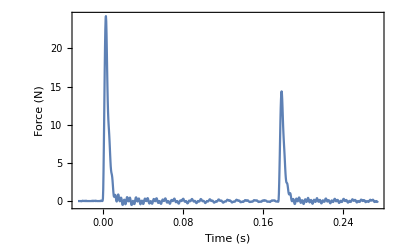
- Zero the force probe.  Press Collect and drop the golf ball through the plastic tube so that it hits the force probe.  
- Export your data into a CVS file and then import it into Mathematica using the Import function. (g1 is to label “golf ball’s 1st trial”)
Example:
fvtg1=Rest[Import[“/home/maryam/Downloads/f1.csv”]]

- Now you can plot your force vs time plot using ListPlot function.
Example:
ListPlot[fvtg1, Joined→True, PlotRange→All, Frame→True, FrameLabel→{“Time (s)”,”Force (N)”}]

-Graphics-

- From the plot find
t0 (* time at which golf ball first hits probe (beginning of the first bounce) *),
t1 (* time at which golf ball leaves probe (end of the first bounce) *),
t2 (* time at which golf ball hits probe for the second time (beginning of the second bounce) *)
and record below.

- Measure m using the scale.

- Measure h using a ruler.  (You may find it convenient to measure the length of the plastic tube and the height of the force probe hook.)

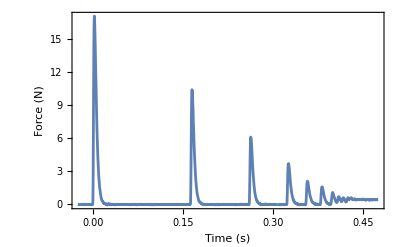

0.0988214

```mathematica
fvtg1 = Rest[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 5\\gballtable1.csv"]];
ListPlot[fvtg1, Joined->True, PlotRange->All, Frame->True, FrameLabel->{"Time (s)","Force (N)"}]
mg1= 0.0458  ;               (* mass of golf ball *)
hg1 = 0.127   ;             (* height that golf ball falls to hit probe *)
t0g1= 0   ;            (* time at which golf ball first hits probe (beginning of the first bounce) *)
t1g1= 0.021   ;            (* time at which golf ball leaves probe (end of the first bounce) *)
t2g1= 0.162   ;         (* time at which golf ball hits probe for the second time (beginning of the second bounce) *)

fg1= Interpolation[fvtg1];
Ipg1= NIntegrate[fg1[t], {t, t0g1, t1g1}]
```

You can find the impulse that force probe delivers to golf ball during the first bounce by integrating force between t0 and t1 using the following two commands,
fg1=Interpolation[fvtg1];
Ipg1=NIntegrate[fg1[t], {t, t0g1, t1g1}]

#### Question 1. - What force(s) are acting on the ball before it hits the probe? - What force(s) are acting on the ball during the first collision, i.e. between t0 and t1? What is their relative sign?

- Before it hits the probe, the only force acting on the ball is the Force of Gravity.
- During the collision, along with the force of gravity pulling the ball downwards (-ve sign), we get a normal force from the probe to the ball, pushing it upwards (+ve).

### Step 2. Calculating the total impulse experienced by the golf ball

- Use kinematic equations to calculate v0 and v1 from information collected in Step 1.  Remember that when you drop the golf ball, it starts at rest.  Be careful with signs: an upward velocity is positive, a downward velocity is negative.

```mathematica
g = 9.81;
v0g1=  -Sqrt[2* g * hg1]       (*velocity of golf ball at time t0*)
v1g1 =  g*(t2g1-t1g1)/2       (*velocity of golf ball at time t1*)
p0g1= mg1 * v0g1 ;        (* momentum of golf ball at time t0*)
p1g1=  mg1 * v1g1  ; (* momentum of golf ball at time t1*)
```

-1.57852

0.691605

#### Question 2. - Use the above information to calculate Ip. Remember that Ip is the impulse for only the force of the probe. - Compare your calculated Ip with the integral of force you calculated in Step 1 and find the percentage error.

The analytical change in impulse on the ball happens to be 0.103972kgms^-1. Assuming Instantanious Gravitational Impulse aproximation to be 0, this also happens to be approximately the Impulse on the force probe
The experimental impulse we get by the software's numerical integration (0.0988214 kgms^-1) has an error of 4.9538% compared to this impulse.

```mathematica
Ipg1A =p1g1-p0g1
ErrorPercg1 = (Ipg1A-Ipg1)*100/Ipg1A
```

0.103972

4.9538

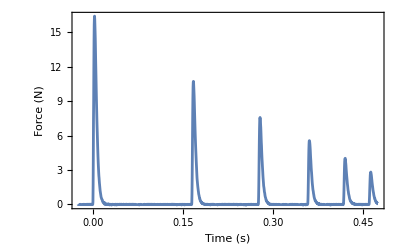

0.0963179

-1.57852

0.70632

0.104646

7.95826

```mathematica
fvtg2 = Rest[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 5\\gballtable2.csv"]];
ListPlot[fvtg2, Joined->True, PlotRange->All, Frame->True, FrameLabel->{"Time (s)","Force (N)"}]
mg2= 0.0458  ;               (* mass of golf ball *)
hg2 = 0.127   ;             (* height that golf ball falls to hit probe *)
t0g2= 0   ;            (* time at which golf ball first hits probe (beginning of the first bounce) *)
t1g2= 0.020   ;            (* time at which golf ball leaves probe (end of the first bounce) *)
t2g2= 0.164   ;         (* time at which golf ball hits probe for the second time (beginning of the second bounce) *)

fg2= Interpolation[fvtg2];
Ipg2= NIntegrate[fg2[t], {t, t0g2, t1g2}]
v0g2=  -Sqrt[2* g * hg2]       (*velocity of golf ball at time t0*)
v1g2 =  g*(t2g2-t1g2)/2       (*velocity of golf ball at time t1*)
p0g2= mg2 * v0g2 ;        (* momentum of golf ball at time t0*)
p1g2=  mg2 * v1g2  ; (* momentum of golf ball at time t1*)
Ipg2A = p1g2-p0g2
ErrorPercg2 = (Ipg2A-Ipg2)*100/Ipg2A
```

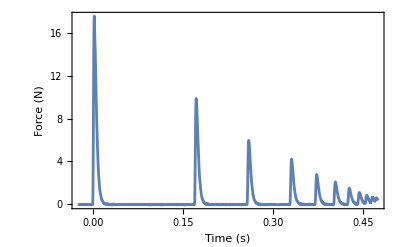

0.100407

-1.57852

0.73575

0.105994

5.27097

```mathematica
fvtg3=Rest[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 5\\gballtable3.csv"]];
ListPlot[fvtg3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Force (N)"}]
mg3=0.0458;               (*mass of golf ball*)
hg3=0.127;             (*height that golf ball falls to hit probe*)
t0g3=0;            (*time at which golf ball first hits probe (beginning of the first bounce)*)
t1g3=0.019;            (*time at which golf ball leaves probe (end of the first bounce)*)
t2g3=0.169;         (*time at which golf ball hits probe for the second time (beginning of the second bounce)*)

fg3=Interpolation[fvtg3];
Ipg3=NIntegrate[fg3[t],{t,t0g3,t1g3}]
v0g3=-Sqrt[2*g*hg3]       (*velocity of golf ball at time t0*)
v1g3=g*(t2g3-t1g3)/2       (*velocity of golf ball at time t1*)
p0g3=mg3*v0g3;        (*momentum of golf ball at time t0*)
p1g3=mg3*v1g3; (*momentum of golf ball at time t1*)
Ipg3A=p1g3-p0g3
ErrorPercg3=(Ipg3A-Ipg3)*100/Ipg3A
```

- If your percentage error is equal to or less than 15%, record your data in the table below. Replace “?” with the corresponding variable from above.
If your percentage error is larger than ~15%, try to find out where the error (systematic error) comes from and discuss it.
Remember that Coefficient Of Restitution (COR) is defined as COR = |normal velocity right after the collision|/|normal velocity right before the collision|.
- Repeat the above steps at least two more times and report the results again on the same table below (you can re-use the code you developed above). In other words, fill out the second and third rows of this table too.

```mathematica
Grid[{{Text["Golf ball, elastic collision"],SpanFromLeft},{"data set","m, kg","t0, s","t1, s","t2, s","h, m", "v0, m/s","v1, m/s", "COR","p1-p0, N*s","∫_t0^t1 F(t)dt, N*s", "(p1 - p0 - SubsuperscriptBox[∫, t0, t1]F (t) dt)/(p1 - p0)*100%"}, 
{"1",mg1,t0g1,t1g1,t2g1,hg1, v0g1,v1g1,-v1g1/v0g1,Ipg1A,Ipg1,ErrorPercg1}, 
{"2",mg2,t0g2,t1g2,t2g2,hg2, v0g2,v1g2,-v1g2/v0g2,Ipg2A,Ipg2,ErrorPercg2}, 
{"3",mg3,t0g3,t1g3,t2g3,hg3, v0g3,v1g3,-v1g3/v0g3,Ipg3A,Ipg3,ErrorPercg3}}, Frame -> All]
```

Golf ball, elastic collision |  |  |  |  |  |  |  |  |  |  | 
data set | m, kg | t0, s | t1, s | t2, s | h, m | v0, m/s | v1, m/s | COR | p1-p0, N*s | ∫_t0^t1 F(t)dt, N*s | (p1 - p0 - SubsuperscriptBox[∫, t0, t1]F (t) dt)/(p1 - p0)*100%
1 | 0.0458 | 0 | 0.021 | 0.162 | 0.127 | -1.57852 | 0.691605 | 0.438134 | 0.103972 | 0.0988214 | 4.9538
2 | 0.0458 | 0 | 0.02 | 0.164 | 0.127 | -1.57852 | 0.70632 | 0.447456 | 0.104646 | 0.0963179 | 7.95826
3 | 0.0458 | 0 | 0.019 | 0.169 | 0.127 | -1.57852 | 0.73575 | 0.4661 | 0.105994 | 0.100407 | 5.27097

### Step 3. Inelastic collision by play-doh ball

Make a play-doh ball of the same mass as the golf ball and repeat steps 1 and 2 above. Record the results in the table below.
Again, you are doing all the steps at least 3 times (i.e., each trial should result in a row in the table below).

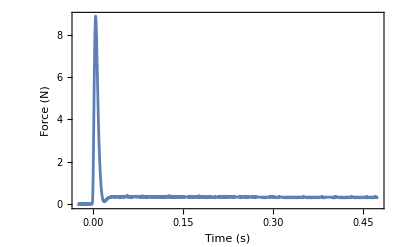

0.0673645

-1.57852

0.083385

0.0761155

11.497

***

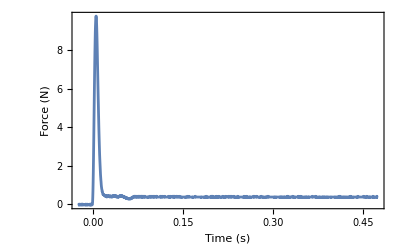

0.0770868

-1.57852

0.063765

0.0752169

-2.486

***

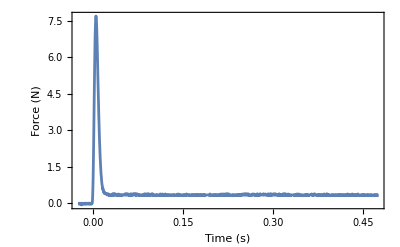

0.0643295

-1.57852

0.073575

0.0756662

14.9825

***

```mathematica
fvtd1=Rest[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 5\\playdoughtable1.csv"]];
ListPlot[fvtd1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Force (N)"}]
md1=0.0458;               (*mass of golf ball*)
hd1=0.127;             (*height that golf ball falls to hit probe*)
t0d1=0;            (*time at which golf ball first hits probe (beginning of the first bounce)*)
t1d1=0.018;            (*time at which golf ball leaves probe (end of the first bounce)*)
t2d1=0.035;         (*time at which golf ball hits probe for the second time (beginning of the second bounce)*)

fd1=Interpolation[fvtd1];
Ipd1=NIntegrate[fd1[t],{t,t0d1,t1d1}]
v0d1=-Sqrt[2*g*hd1]       (*velocity of golf ball at time t0*)
v1d1=g*(t2d1-t1d1)/2       (*velocity of golf ball at time t1*)
p0d1=md1*v0d1;        (*momentum of golf ball at time t0*)
p1d1=md1*v1d1; (*momentum of golf ball at time t1*)
Ipd1A=p1d1-p0d1
ErrorPercd1=(Ipd1A-Ipd1)*100/Ipd1A

"***"

fvtd2=Rest[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 5\\playdoughtable2.csv"]];
ListPlot[fvtd2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Force (N)"}]
md2=0.0458;               (*mass of golf ball*)
hd2=0.127;             (*height that golf ball falls to hit probe*)
t0d2=0;            (*time at which golf ball first hits probe (beginning of the first bounce)*)
t1d2=0.019;            (*time at which golf ball leaves probe (end of the first bounce)*)
t2d2=0.032;         (*time at which golf ball hits probe for the second time (beginning of the second bounce)*)

fd2=Interpolation[fvtd2];
Ipd2=NIntegrate[fd2[t],{t,t0d2,t1d2}]
v0d2=-Sqrt[2*g*hd2]       (*velocity of golf ball at time t0*)
v1d2=g*(t2d2-t1d2)/2       (*velocity of golf ball at time t1*)
p0d2=md2*v0d2;        (*momentum of golf ball at time t0*)
p1d2=md2*v1d2; (*momentum of golf ball at time t1*)
Ipd2A=p1d2-p0d2
ErrorPercd2=(Ipd2A-Ipd2)*100/Ipd2A

"***"

fvtd3=Rest[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 5\\playdoughtable3.csv"]];
ListPlot[fvtd3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Force (N)"}]
md3=0.0458;               (*mass of golf ball*)
hd3=0.127;             (*height that golf ball falls to hit probe*)
t0d3=0;            (*time at which golf ball first hits probe (beginning of the first bounce)*)
t1d3=0.019;            (*time at which golf ball leaves probe (end of the first bounce)*)
t2d3=0.034;         (*time at which golf ball hits probe for the second time (beginning of the second bounce)*)

fd3=Interpolation[fvtd3];
Ipd3=NIntegrate[fd3[t],{t,t0d3,t1d3}]
v0d3=-Sqrt[2*g*hd3]       (*velocity of golf ball at time t0*)
v1d3=g*(t2d3-t1d3)/2       (*velocity of golf ball at time t1*)
p0d3=md3*v0d3;        (*momentum of golf ball at time t0*)
p1d3=md3*v1d3; (*momentum of golf ball at time t1*)
Ipd3A=p1d3-p0d3
ErrorPercd3=(Ipd3A-Ipd3)*100/Ipd3A

"***"
```

```mathematica
Grid[{{Text["Play-doh ball, inelastic collision"],SpanFromLeft},{"data set","m, kg","t0, s","t1, s","t2, s","h, m", "v0, m/s","v1, m/s", "COR","p1-p0, N*s","∫_t0^t1 F(t)dt, N*s", "(p1 - p0 - SubsuperscriptBox[∫, t0, t1]F (t) dt)/(p1 - p0)*100%"}, {"1",md1,t0d1,t1d1,t2d1,hd1, v0d1,v1d1,-v1d1/v0d1,Ipd1A,Ipd1,ErrorPercd1}, 
{"2",md2,t0d2,t1d2,t2d2,hd2, v0d2,v1d2,-v1d2/v0d2,Ipd2A,Ipd2,ErrorPercd2}, 
{"3",md3,t0d3,t1d3,t2d3,hd3, v0d3,v1d3,-v1d3/v0d3,Ipd3A,Ipd3,ErrorPercd3}}, Frame -> All]
```

Play-doh ball, inelastic collision |  |  |  |  |  |  |  |  |  |  | 
data set | m, kg | t0, s | t1, s | t2, s | h, m | v0, m/s | v1, m/s | COR | p1-p0, N*s | ∫_t0^t1 F(t)dt, N*s | (p1 - p0 - SubsuperscriptBox[∫, t0, t1]F (t) dt)/(p1 - p0)*100%
1 | 0.0458 | 0 | 0.018 | 0.035 | 0.127 | -1.57852 | 0.083385 | 0.0528246 | 0.0761155 | 0.0673645 | 11.497
2 | 0.0458 | 0 | 0.019 | 0.032 | 0.127 | -1.57852 | 0.063765 | 0.0403953 | 0.0752169 | 0.0770868 | -2.486
3 | 0.0458 | 0 | 0.019 | 0.034 | 0.127 | -1.57852 | 0.073575 | 0.04661 | 0.0756662 | 0.0643295 | 14.9825

#### Question 3. - Calculate the coefficient of restitution (COR) for the golf ball and play-doh ball. - Compare to the COR value you obtained in Lab2.

The Coefficient of restitution is defined as the (velocity of separation)/(velocity of approach) = -v1/v0

The mean COR for golfball is 0.450563 and that of the do-ball is 0.04661.

Although this is way different (almost half) of what we got for lab 2, it is still consistent with the setup in a sense that the golfball has a significantly higher COR than the doball and hence bounces back up whereas the do-ball sticks to the surface.

```mathematica
Mean[{0.4381338041226227, 0.44745579995501894, 0.46609979161981135}]
Mean[{0.0528246430502453, 0.04039531527371698,0.04660997916198114}]
```

0.450563

0.04661

#### Question 4. - Discuss why the following two statements are incorrect: A. The clay ball will exert the greater force because it has to be stopped, while the golf ball retains most of its speed. B. The balls will exert the same force, because they have the same mass and are moving at the same speed right before the first collision.

The clay ball does stop and the golf ball does retain a significant amount of its speed but that means there is a Greater Impulse on golf ball and not the clayball. Hence, the force exerted on the clay ball is Smaller than that on the golf ball.

 The force depends on the time of collision as well as the velocity after the collision and not just the speed and mass before.
 (Essentially the impulse and the time). Because the velocity of the clay drops off quickly, it has a lower impulse. As for the golf ball, not only does the velocity drop down, it also picks up speed in the opposite direction. Hence the impulse is higher for the golf ball. So is the force.

## Part II. The Cart, The Motion Sensor, & The Force Sensor

In the second part we will make a similar measurement with a rolling cart hitting the force probe. For this part, you will work together with another lab group. One group measures the force exerted by the rolling cart, the other group measures the velocity of the cart before and after the collision using a motion detector. 
ATTENTION: Members of both group have to save the data from the Force probe and the Motion detector. You will have to use these data in your next  lab’s prerequisite assignment!

### Step 1. Elastic Collision, Collecting Data

- Put the cart on the track between the force probe and the motion detector. The motion detector and the force probe should both be facing towards the cart.  
- Move the force probe such that it is parallel to the track at a position such that it will hit the cart close to the center.
- Set the motion detector of the group at the adjacent table on the track. 
- Make a few test runs and be sure the motion detector follows the cart until it hits the force probe. BE GENTLE! Do not push the cart too quickly.
- When the cart hits the probe, one group member should be holding the probe tightly, so that it does not recoil.
- Zero the force probe, press Collect on both computers, and set the cart in motion, so that it hits the force probe and bounces back. 
- Repeat until you get a smooth curve for the position of the cart. 
- Export your data from the force probe and motion detector into CVS format.
- Save the collected data files to be used in your next lab’s prerequisite assignment (see below).

### Step 2. Elastic Collision, Measuring Impulse, Using Force Data & Using Velocity Data

## Prerequisite Assignment for Collision II lab Please submit together with Collision I lab report.

#### Calculating the Impulse

- Import the force detector data from .csv file. 
- Plot the F(t) data showing the collision.
- Determine the time before and after collision.
- Calculate the impulse Ipc delivered by probe on the cart by integrating force vs time over the collision time period. You can use example for the golf ball.

#### Calculating velocities and the change in momentum

- Import displacement and velocity vs time data from the .csv file -- this is data recorder by the motion detector.
Example code:
x=Rest[Part[Import[“/home/maryam/Documents/275_f14/Lab5/velocity.csv”],All,{1,2}]];
v=Rest[Part[Import[“/home/maryam/Documents/275_f14/Lab5/velocity.csv”],All,{1,3}]];
In the lines above, the “Part” function separates your data into 2 files: position vs time, and velocity vs time.
 
- Now you can plot the position vs time plot using ListPlot:
ListPlot[x]

- Use Get Coordinates tool to determine the time of collision t1. It is essential that the time is accurately determined. 

- The cart has a small acceleration caused by small ‘rolling friction’ of its wheels and some air drag. We will consider a uniform acceleration approximation for the cart’s motion. Remember that for a uniform acceleration a, x(t) = x0 + v0*t + 0.5*a*t^2, and that v(t) = ∂_t x(t). Therefore, we will make a parabolic fit to the position vs time graph to determine the x(t) function. We do this separately for “before” and “after” the collision time periods. Then, we will calculate the velocity just before and right after the collision.

- Present your results for vi and vf (velocity before and after the collision) in a table format. 

Below is an example of results for vi and vf calculation:

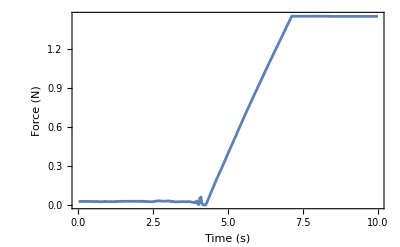

```mathematica
x=Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\cartposition2.csv"],All,{1,2}]];
v=Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\cartforce2.csv"],All,{1,2}]];
ListPlot[x,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Force (N)"}]
```

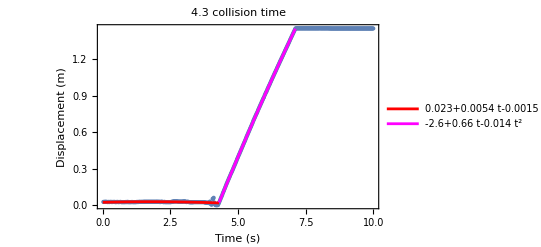

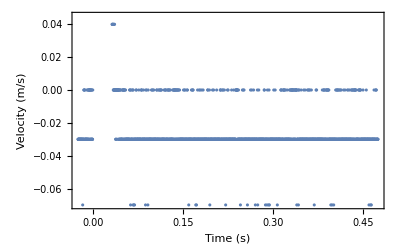

```mathematica
t0 = 0;
t1 = 4.3;
t2 = 7.12;
line1=Fit[Select[x, t0<First[#]<t1-.05&],{1,t,t^2},t]; (* makes a parabolic fit to the data between t0 and t1-0.05 s *)
line2=Fit[Select[x, t1+.05<First[#]<t2&],{1,t,t^2},t];
vi=D[line1, t] /. t->t1; (* calculates velocity at the moment t1 *)
vf=D[line2, t] /. t->t1;
Show[ListPlot[x],Plot[line1,{t,0,t1},PlotStyle->Red, PlotLegends-> {NumberForm[line1,2], ""}], Plot[line2,{t,t1,t2},PlotStyle->Magenta, PlotLegends->{ NumberForm[line2,2],""}], PlotLabel-> "collision time" t1 , Frame->True, FrameLabel->{"Time (s)","Displacement (m)"}]
ListPlot[v,Frame->True, FrameLabel->{"Time (s)","Velocity (m/s)"}]
Grid[{{Text["collision time" t1],SpanFromLeft},{"vi, m/s","vf, m/s"}, {NumberForm[vi,3],NumberForm[vf,3]}}, Frame -> All]
```

```mathematica
{{4.3 "collision time", }, {"vi, m/s", "vf, m/s"}, {-0.03, 0.03}}
```

#### Testing the relation: the change in momentum = impulse

Calculate and record the results in the table below.

```mathematica
Grid[{{Text["Cart, Elastic collision"],SpanFromLeft},{"m, kg","vi, m/s","vf, m/s", "COR","pf-pi, N*s","Ipc=∫_(t1 - 0.1)^(t1 + 0.1) F(t)dt, N*s", "(pf - pi - Ipc)/(pf - pi)*100%"}, 
{""3.0 ± 0.50"","","?","?","?", "?","?"}}, Frame -> All]
```

Cart, Elastic collision |  |  |  |  |  | 
m, kg | vi, m/s | vf, m/s | COR | pf-pi, N*s | Ipc=∫_(t1 - 0.1)^(t1 + 0.1) F(t)dt, N*s | (pf - pi - Ipc)/(pf - pi)*100%
3.0 ± 0.50 | ? | ? | ? | ? | ? | ?

Rutgers 275 Classical Physics Lab
“Collisions-I” and “Collisions-II”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014 (edited by V. Podzorov, 2023)